# 11. Least Squares

## Linear Interpolation

At the start of linear algebra we are always looking for square systems of linear equations: 
	m equations for n=m unknowns

We looked at interpolation earlier:  The task is to find a weighted linear combination
	f(x)=a_1 f_1(x)+a_2 f_2(x)+…+a_n f_n(x)=∑_(j=1)^n a_j f(x)  
of n=m given functions f_1,f_2,…,f_n that interpolate m point-value pairs 
	(x_1,y_1)
	(x_2,y_2)
	     ⋮
	(x_m,y_m) 
In the sense that f(x_i)=y_i for i=1…m.

If each y_i is a scalar then each  f(x_i)=y_i is a single scalar equation for the n=m vector a={a_1,a_2,…,a_n} of unknowns.

Arranging this in the standard way gives the square system of linear equations A.a=y for a where

A_ij=f_j(x_i) and y={y_1,y_2,…,y_m}

Row i of the matrix is the coefficients for equation i

Column j of the matrix is associated with variable a_j.

The example we did before had polynomials and it applies just the same way to sums of trig functions! It is actually much more general than you might think. For instance it applies to the set of Radial Basis Functions defined by 
	f_i(x)=ϕ(||x-c_i||)
for a set of centers c_i∈Ω⊂ℝ^2 and the Gaussian “shape function” ϕ(r)=ⅇ^(-r^2).

## Least Squares Fit

We are are going to wind up trying to satisfy a Tall-Skinny system of linear equations: 
	m equations for n unknowns: A∈ℝ^(m×n)with m>n

We are going to revisit interpolation:  The task is to find a weighted linear combination
	f(x)=a_1 f_1(x)+a_2 f_2(x)+…+a_n f_n(x)=∑_(j=1)^n a_j f(x_j)  
of n given functions f_1,f_2,…,f_n that interpolate m point-value pairs 
	(x_1,y_1)
	(x_2,y_2)
	     ⋮
	(x_m,y_m) 
In the sense that f(x_i)≈y_i for i=1…m.  We can no longer ask for equality!

If each y_i is a scalar then each  f(x_i)=y_i is a single scalar equation for the n vector a={a_1,a_2,…,a_n} of unknowns.

Arranging this in the standard way gives the Tall Skinny system of linear equations A.a≈y for a where

A_ij=f_j(x_i) and y={y_1,y_2,…,y_n}

Row i of the matrix is the coefficients for equation i.  There are m rows.

Column j of the matrix is associated with variable a_j.  There are n columns.

Since m>n the matrix A is Tall and Skinny: there are more equations than variables

We need to work out what it means to solve a Tall-Skinny system of linear equations!

## “Solving” Tall-Skinny Linear Systems: A.x=b

If A∈ℝ^(m×n) is tall and skinny then m>n.  Each row is an equation and each column is associated with an unknown: We have more equations the unknowns.  From linear algebra we know that we can not (in general) hope to solve all the equations! The standard solution is to minimize the Euclidean 2-norm ||b-A.x|| or equivalently || b - A . x (||)^2 . The mismatch b-A.x is called the residual.

We are going to see several ways of doing this! As always, some are more expensive than others. As always, some are better than others.

As a formula we are looking for 
	x_*=argmin_(x∈ ℝ^n)||A.x-b(||)^2
In words, we are looking for the point nearest b in the range of A or equivalently the column space of A.

### QR Decomposition

We just finished working out how to compute QR decomposition A=Q.R that give us Q which is an orthogonal basis for the column space of a tall-skinny matrix A. If we bothered to compute it we also got an orthogonal basis H for the full space ℝ^m satisfying A=H.(R
0) so we have
	||b-A.x(||)^2=||b-H.(R
0).x(||)^2=||Hᵀ.b-Hᵀ.H.(R
0).x(||)^2=||Hᵀ.b-(R
0).x(||)^2=||Hᵀ.b-(R
0).x(||)^2
The last thing to do is realize that the squared two-norm splits into a top-bit
	∑_(i=1)^n |(Hᵀ.b)_i-(R.x)_i|^2=∑_(i=1)^n |(Qᵀ.b)_i-(R.x)_i|^2=||Qᵀ.b-R.x(||)^2 
and a bottom bit
	∑_(i=n+1)^m |(Hᵀ.b)_i|^2
which does not depend on x.  Since R is square and upper triangular it is simple to solve 
	  R.x=Qᵀ.b
for the least squares solution x_*. You evaluate the quality of x_* using the residual ||b-A.x_*(||)_2.

### SVD Decomposition

Although we do not yet know how it is computed the thick SVD gives the decomposition
	A=U.Σ.Vᵀ
where U is an orthogonal basis for ℝ^m, V is an orthogonal basis for ℝ^n, the m×n diagonal matrix Σ has the singular values σ_i in non-increasing order on the diagonal, and the rank r is the number of non-zero singular values. The thin SVD
	A=Û.Σ̂.V̂ ᵀ
is simply the m×r Û=U⟦All,1; ;r⟧ (an orthogonal basis for the column space of A), the n×r matrix V̂=V⟦All,1; ;r⟧, and the r×r diagonal matrix  Σ̂=Σ⟦1; ;r,1; ;r⟧ as a result,   
	||b-A.x(||)^2=||b-U.Σ.Vᵀ.x(||)^2=||Uᵀ.b-Uᵀ.U.Σ.Vᵀ.x(||)^2=||Uᵀ.b-Σ.Vᵀ.x(||)^2
and the squared two-norm splits into a bit that depends on x 
	∑_(i=1)^r |(Uᵀ.b)_i-(σ_i(Vᵀ.x))_i|^2=||Û ᵀ.b-Σ̂.V̂ ᵀ.x(||)^2
and a left over bit (remember in the thick SVD σ_i=i for i>r) which does not depend on x.  The minimum occurs when
	V̂ ᵀ.x=(Σ̂)^-1.Û ᵀ.b ⟹x=V̂.OverHat[(Σ)]^-1.Û ᵀ.b
The expression V̂.OverHat[(Σ)]^-1.Û ᵀ is called the Moore-Penrose Pseudo Inverse of A and is written A^†.

### Explicit Projection

The last argument is geometrical. Just in case we forgot, the orthogonal projection onto the column space of a tall-skinny m×n real matrix A is 
	P=A.(Aᵀ.A)^-1.Aᵀ.
If x minimizes ||r(||)^2=||b-A.x(||)^2 then r must be orthogonal to the range of A. This means that
	Aᵀ.r=0 ⟹ Aᵀ.A.x=Aᵀ.b
If A is full rank (i.e rank n) then Αᵀ.A is invertible and we can solve to get 
	x_*=(Aᵀ.A)^-1.Aᵀ.b.

### Verification

These all give the same answer just like they should!

```mathematica
{m,n}={12,3};A = RandomReal[{-1,1},{m,n}]; b =RandomReal[{-1,1},m];
(* QR Technique *)
{Q,R}=QRDecomposition[A];Q=Qᵀ;
xQR=LinearSolve[R,Qᵀ.b]
(* SVD technique.  I get the thin SVD by asking for the appropriate rank. *)
{U,S,V}= SingularValueDecomposition[A,n];
xSVD=V.Inverse[S].Uᵀ.b
(* Projection Technique *)
xPRO=Inverse[Aᵀ.A].Aᵀ.b
(* Explicit Pseudo Inverse *)
xPIN=PseudoInverse[A].b
```

{0.404331,0.921182,-0.149196}

{0.404331,0.921182,-0.149196}

{0.404331,0.921182,-0.149196}

«1 more identical outputs»

## Data Fitting

We want to find the best weighted linear combination
	f(x)=a_1 f_1(x)+a_2 f_2(x)+…+a_n f_n(x)=∑_(j=1)^n a_j f(x_j)  
to the data 
	(x_1,y_1)
	(x_2,y_2)
	     ⋮
	(x_m,y_m) 
In the sense that the error ∑_(i=1)^n (f(x_i)-y_i)^2 is as small as possible. The solution is simple:

Define the matrix m×n matrix A where A_(i,j)=f_j(x_i) and the m vector b where b_i=y_i.

Compute a_*=argmin_a||b-A.a|| using any of the above techniques. Substitute optimal parameters into sum for optimal f(x).

### Polynomial Fitting

{0.844372,0.483406,-1.14241,0.754868,-0.178835,0.0490376}

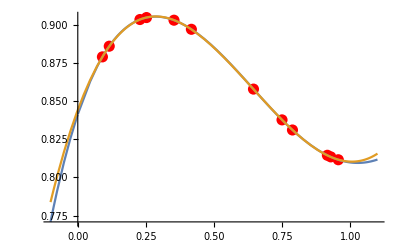

```mathematica
{m,n}={12,6};
g[x_]:= Sin[x+Cos[Sin[x]+ArcTan[x]]]
xs= RandomReal[{0,1},m];
fs[x_]:=Table[x^j,{j,0,n-1}]
A=Map[fs,xs];
b=Map[g,xs];
as=PseudoInverse[A].b
f[x_]:=as.fs[x]
Plot[{g[x],f[x]},{x,-0.1,1.1},
Prolog->{Red, PointSize[0.02],Point[{xs,b}ᵀ]}]
```

### Trig Fitting

{231.561,-439.138,378.339,-294.126,205.25,-127.568,69.7395,-32.9413,13.059,-4.14722,0.95964,-0.129598}

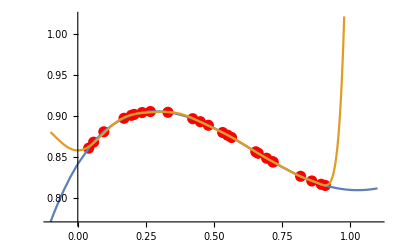

```mathematica
{m,n}={24,12};
g[x_]:= Sin[x+Cos[Sin[x]+ArcTan[x]]]
xs= RandomReal[{0,1},m];
fs[x_]:=Table[Cos[ 2 j x],{j,0,n-1}]
A=Map[fs,xs];
b=Map[g,xs];
as=PseudoInverse[A].b
f[x_]:=as.fs[x]
Plot[{g[x],f[x]},{x,-0.1,1.1},
Prolog->{Red, PointSize[0.02],Point[{xs,b}ᵀ]}]
```

### RBF Fitting

```mathematica
{m,n}={123,56};
g[{x1_,x2_}]:= Sin[x1+Cos[Sin[x2]+ArcTan[x1]]]
Omega=RegionUnion[Disk[{0,0},2],Disk[{1,1},1.6], Rectangle[{1,1.6},{3,3.6}]];
xs= RandomPoint[Omega,m];
ys=Map[g,xs];
points3D=Table[Flatten[{xs⟦i⟧,ys⟦i⟧}],{i,m}];
ϕ[r_]:=E^(-r^2)
fs[{x1_,x2_}]:=Table[ϕ[Norm[{x1,x2}-xs⟦j⟧]],{j,1,n}]
A=Map[fs,xs];
b=Map[g,xs];
as=PseudoInverse[A].b
f[x_]:=as.fs[x]
Show[
ListPointPlot3D[points3D,PlotStyle->Red],
Plot3D[{f[{x1,x2}],g[{x1,x2}]},{x1,x2}∈Omega,
PlotRange->All]
]
```

{1.24582,-15.7074,-111.126,7.4631,-1.03465,-1.10251,-3.63942,8.27581,9.95493,6.03359,-3.83241,3.09038,-4.28857,9.0689,2.68883,2.43244,2.34092,-7.47502,2.74502,10.0154,2.15692,108.108,-0.864073,-0.272739,-3.68411,-6.49356,-6.411,88.0913,0.944642,1.52204,-0.569993,-2.69669,-0.0702916,4.89926,-5.01434,0.352206,1.80612,-11.1487,-1.49486,21.2103,5.82142,3.15272,-0.500353,-17.5308,2.37349,-56.7885,-0.734822,3.23726,22.9175,0.765813,2.77004,-0.522348,-40.1399,-19.9173,-5.44123,-4.31368}

-Graphics3D-

```mathematica
g[{0.2,0.3}]
f[{0.2,0.3}]
```

0.882408

0.344573